```mathematica
ClearAll["Global`*"]
```

```mathematica
PathMD="/Volumes/Backup/YosemiteFiles/MEGAsync/Density_Profiles/ptensor/ptensor_density_profiles/";
```

```mathematica
L={6.77155,6.7869,6.67282,6.61698,6.52151,6.49091,6.43758}
```

```mathematica
{6.77155,6.7869,6.67282,6.61698,6.52151,6.49091,6.43758}
```

{6.77155,6.7869,6.67282,6.61698,6.52151,6.49091,6.43758}

```mathematica
SAM 0%
```

```mathematica
With Number Density
```

We store the water NUMBER density of SAM 0 % in nWaterdata0

```mathematica
input = Import[PathMD<>"ndens_NPT_sam0_water_ptensor.xvg","Table"];
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
nWaterData0 = Take[input,{start+1,Length[input]}]; (* extracted data *)
nWaterData0[[All,2]]=nWaterData0[[All,2]]/3;
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}];
```

We store the surface NUMBER density of SAM 0 % in nSurfData0

```mathematica
input = Import[PathMD<>"ndens2_NPT_sam0_water_ptensor.xvg","Table"];
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
nSurfData0 = Take[input,{start+1,Length[input]}]; (* extracted data *)
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

We plot the density maps together to determine the bulk intervals. The plot is called plotNum0. We also zoom into the interface region in the plot called plotNum0Zoom.

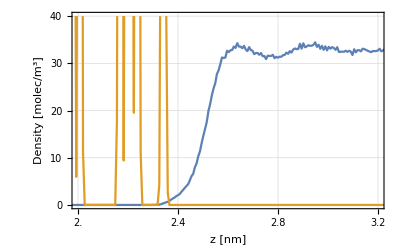

```mathematica
plotNum0=ListPlot[{nWaterData0,nSurfData0},Joined->True,Frame->True,PlotRange->All,GridLines->None];
plotNum0Zoom=ListPlot[{nWaterData0,nSurfData0},Joined->True,PlotRange->{{2,3.2},{0,40}},GridLines->Automatic,Frame->{{True,True},{True,True}},FrameTicks->{{2.0,2.4,2.8,3.2},{0,10,20,30,40},{None},{None}},FrameLabel->{"z [nm]","Density [molec/m^3]"},LabelStyle->{FontSize->15}];
(*GraphicsGrid[{{plotNum0Zoom,plotNum0}}]*)
(*LabelStyle->{GrayLevel[0],Bold}*)
Show[plotNum0Zoom,Prolog->{Inset[plotNum0,{3.15,0},{Right,Bottom},0.5,Background->White]},PlotLabel->None]
(*PlotStyle->{{Automatic},{Gray}}*)
```

```mathematica
(*Another Way to Use Inset!!!
g=Plot[x ^2,{x,0,100},Prolog->{Inset[plotNum0,{100,200},{Right,Bottom},50]}]*)
```

We calculate the BULK value of the water and the surface as the average of the NON-ZERO density data points. The results are stored in the variables positive0waterN and positive0samN

```mathematica
sum0Nw=0;points=0;Do[If[nWaterData0[[i,2]]≠0,sum0Nw=sum0Nw+nWaterData0[[i,2]];points=points+1],{i,1,Length[nWaterData0]}]
positive0waterN=sum0Nw/points;
Print["water: average of non-negative density = ",positive0waterN]
sum0Ns=0;points=0;Do[If[nSurfData0[[i,2]]≠0,sum0Ns=sum0Ns+nSurfData0[[i,2]];points=points+1],{i,1,Length[nSurfData0]}]
positive0samN=sum0Ns/points;
Print["surface: average of non-negative density = ",positive0samN]
```

water: average of non-negative density = 29.7932

surface: average of non-negative density = 377.984

The MEAN values are stored in the variables mean0waterN and mean0samN

```mathematica
mean0waterN = Mean[nWaterData0[[All,2]]];
Print["water: mean value of number density = ",mean0waterN]
mean0samN = Mean[nSurfData0[[All,2]]];
Print["surface: mean value of number density = ",mean0samN]
```

water: mean value of number density = 19.9019

surface: mean value of number density = 42.3343

The MEAN value of the water density inside an INTERVAL is stored in the variable bulk0waterN . We specifiy the start and end position of the interval.

```mathematica
start=3.5;
end=6;
densDummy=nWaterData0[[All,2]];
posDummy=nWaterData0[[All,1]];
lastPos=posDummy[[-1]]+posDummy[[2]];
intervals=Length[densDummy];
startpos=Round[((start/lastPos)*intervals)+1];
endpos=Round[((end/lastPos)*intervals)+1];
bulk0waterN = Mean[densDummy[[startpos;;endpos]]];
Print["water: mean value of num density = ",bulk0waterN]
```

water: mean value of num density = 32.8158

The MEAN value of the surface density an INTERVAL is stored in the variable bulk0surfN . We specifiy the start and end position of the interval.

```mathematica
start=1.0;
end=2.0;
densDummy=nSurfData0[[All,2]];
posDummy=nSurfData0[[All,1]];
lastPos=posDummy[[-1]]+posDummy[[2]];
intervals=Length[densDummy];
startpos=Round[((start/lastPos)*intervals)+1];
endpos=Round[((end/lastPos)*intervals)+1];
bulk0surfN = Mean[densDummy[[startpos;;endpos]]];
Print["surface: mean value of num density = ",bulk0surfN]
```

surface: mean value of num density = 134.491

INTEGRAL over the WATER is stored in variable sum0waterN.

```mathematica
sum0waterN=Integrate[Interpolation[nWaterData0][x],{x,0,6.0}]/bulk0waterN;
Print["water: Integral/Mean = ",sum0waterN]
```

water: Integral/Mean = 3.49721

```mathematica
L0=Integrate[1,{x,0,6.0}]
```

6.

```mathematica
GDS0N=L0-sum0waterN
```

2.50279

```mathematica
LineGDS0=Line[{{GDS0N,0},{GDS0N,1500}}]
LineBulk0=Line[{{0,bulk0waterN},{3.2,bulk0waterN}}]
```

Line[{{2.50279,0},{2.50279,1500}}]

Line[{{0,32.8158},{3.2,32.8158}}]

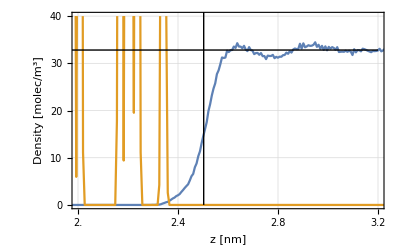

```mathematica
plotNum0GDS=ListPlot[{nWaterData0,nSurfData0},Joined->True,Joined->True,PlotRange->{{2,3.2},{0,40}},GridLines->Automatic,Frame->{{True,True},{True,True}},FrameTicks->{{2.0,2.4,2.8,3.2},{0,10,20,30,40},{None},{None}},FrameLabel->{"z [nm]","Density [molec/m^3]"},LabelStyle->{FontSize->15},Epilog->{LineGDS0,LineBulk0}];
Show[plotNum0GDS,Prolog->{Inset[plotNum0,{3.15,0},{Right,Bottom},0.5,Background->White]},PlotLabel->None]
```

INTEGRAL over the SURFACE is stored in variable sum0samN.

```mathematica
sum0samN=Integrate[Interpolation[nSurfData0][x],{x,0,L0}]/bulk0surfN;
Print["surface: Integral/Bulk = ",sum0samN]
```

surface: Integral/Bulk = 2.11084

```mathematica
(*sum0samN=Integrate[Interpolation[nSurfData0][x],{x,0,L0}]/positive0samN;
Print["surface: Integral/Bulk = ",sum0samN]*)
```

The DEPLETION layer is stored in variable d0N.

```mathematica
depletionDouble0N=L0-sum0waterN-sum0samN
```

0.391943

```mathematica
d0N=depletionDouble0N/2
```

0.195972

Line[{{2.11084,0},{2.11084,1500}}]

Line[{{2.50279,0},{2.50279,1500}}]

Line[{{0,134.491},{6.,134.491}}]

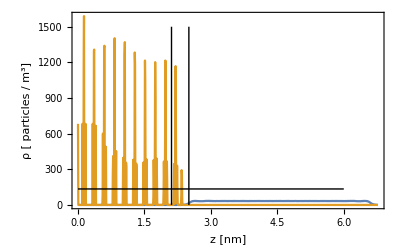

```mathematica
LineGDSSAM0=Line[{{sum0samN,0},{sum0samN,1500}}]
LineDepSAM0=Line[{{sum0samN+depletionDouble0N,0},{sum0samN+depletionDouble0N,1500}}]
LineBulkSAM0=Line[{{0,bulk0surfN},{L0,bulk0surfN}}]
plotNumSAM0=ListPlot[{nWaterData0,nSurfData0},Joined->True,Frame->True,FrameLabel->{"z [nm]","ρ [ particles / m^3]"},PlotRange->All,GridLines->None,Epilog->{LineGDSSAM0,LineBulkSAM0,LineDepSAM0}]
```

```mathematica
SAM 5%
```

We store the water NUMBER density of SAM 5 % in nWaterdata5

```mathematica
input = Import[PathMD<>"ndens_NPT_sam5_water_ptensor.xvg","Table"];
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
nWaterData5 = Take[input,{start+1,Length[input]}]; (* extracted data *)
nWaterData5[[All,2]]=nWaterData5[[All,2]]/3;
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

We store the surface NUMBER density of SAM 5 % in nSurfData5

```mathematica
input = Import[PathMD<>"ndens2_NPT_sam5_water_ptensor.xvg","Table"];
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
nSurfData5 = Take[input,{start+1,Length[input]}]; (* extracted data *)
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

We plot the density maps together to determine the bulk intervals. The plot is called plotNum5. We also zoom into the interface region in the plot called plotNum5Zoom.

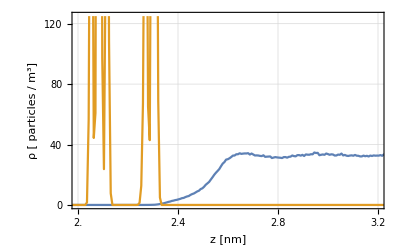

```mathematica
plotNum5=ListPlot[{nWaterData5,nSurfData5},Joined->True,Frame->True,PlotRange->All,GridLines->None];
plotNum5Zoom=ListPlot[{nWaterData5,nSurfData5},Joined->True,PlotRange->{{2,3.2},{0,125}},GridLines->Automatic,Frame->{{True,True},{True,True}},FrameTicks->{{2.0,2.4,2.8,3.2},{0,40,80,120},{None},{None}},FrameLabel->{"z [nm]","ρ LabelStyle→{GrayLevel[0],Bold}"},LabelStyle->{GrayLevel[0]}];
(*GraphicsGrid[{{plotNum5Zoom,plotNum5}}]*)
Show[plotNum5Zoom,Prolog->{Inset[plotNum5,{3.15,0},{Right,Bottom},0.5,Background->White]},PlotLabel->None,FrameLabel->{"z [nm]","ρ [ particles / m^3]"},LabelStyle->{GrayLevel[0]}]
(*PlotStyle->{{Automatic},{Gray}}*)
```

```mathematica
(*Another Way to Use Inset!!!
g=Plot[x ^2,{x,0,100},Prolog->{Inset[plotNum5,{100,200},{Right,Bottom},50]}]*)
```

We calculate the BULK value of the water and the surface as the average of the NON-ZERO density data points. The results are stored in the variables positive5waterN and positive5samN

```mathematica
sum5Nw=0;points=0;Do[If[nWaterData5[[i,2]]≠0,sum5Nw=sum5Nw+nWaterData5[[i,2]];points=points+1],{i,1,Length[nWaterData5]}]
positive5waterN=sum5Nw/points;
Print["water: average of non-negative density = ",positive5waterN]
sum5Ns=0;points=0;Do[If[nSurfData5[[i,2]]≠0,sum5Ns=sum5Ns+nSurfData5[[i,2]];points=points+1],{i,1,Length[nSurfData5]}]
positive5samN=sum5Ns/points;
Print["surface: average of non-negative density = ",positive5samN]
```

water: average of non-negative density = 29.3925

surface: average of non-negative density = 359.071

The MEAN values are stored in the variables mean5waterN and mean5samN

```mathematica
mean5waterN = Mean[nWaterData5[[All,2]]];
Print["water: mean value of number density = ",mean5waterN]
mean5samN = Mean[nSurfData5[[All,2]]];
Print["surface: mean value of number density = ",mean5samN]
```

water: mean value of number density = 19.8399

surface: mean value of number density = 44.1658

The MEAN value of the water density inside an INTERVAL is stored in the variable bulk5waterN . We specifiy the start and end position of the interval.

```mathematica
start=3.5;
end=6;
densDummy=nWaterData5[[All,2]];
posDummy=nWaterData5[[All,1]];
lastPos=posDummy[[-1]]+posDummy[[2]];
intervals=Length[densDummy];
startpos=Round[((start/lastPos)*intervals)+1];
endpos=Round[((end/lastPos)*intervals)+1];
bulk5waterN = Mean[densDummy[[startpos;;endpos]]];
Print["water: mean value of num density = ",bulk5waterN]
```

water: mean value of num density = 32.8104

The MEAN value of the surface density an INTERVAL is stored in the variable bulk5surfN . We specifiy the start and end position of the interval.

```mathematica
start=1.0;
end=2.0;
densDummy=nSurfData5[[All,2]];
posDummy=nSurfData5[[All,1]];
lastPos=posDummy[[-1]]+posDummy[[2]];
intervals=Length[densDummy];
startpos=Round[((start/lastPos)*intervals)+1];
endpos=Round[((end/lastPos)*intervals)+1];
bulk5surfN = Mean[densDummy[[startpos;;endpos]]];
Print["surface: mean value of num density = ",bulk5surfN]
```

surface: mean value of num density = 123.231

INTEGRAL over the WATER is stored in variable sum5waterN.

```mathematica
sum5waterN=Integrate[Interpolation[nWaterData5][x],{x,0,6.0}]/bulk5waterN;
Print["water: Integral/Mean = ",sum5waterN]
```

water: Integral/Mean = 3.48898

```mathematica
L5=Integrate[1,{x,0,6.0}]
```

6.

```mathematica
GDS5N=L5-sum5waterN
```

2.51102

```mathematica
LineGDS5=Line[{{GDS5N,0},{GDS5N,1500}}]
LineBulk5=Line[{{0,bulk5waterN},{3.2,bulk5waterN}}]
```

Line[{{2.51102,0},{2.51102,1500}}]

Line[{{0,32.8104},{3.2,32.8104}}]

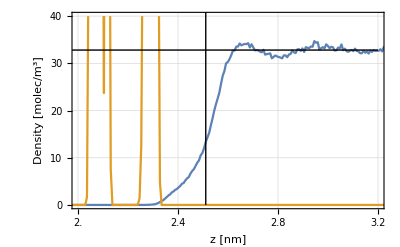

```mathematica
plotNum5GDS=ListPlot[{nWaterData5,nSurfData5},Joined->True,Joined->True,PlotRange->{{2,3.2},{0,40}},GridLines->Automatic,Frame->{{True,True},{True,True}},FrameTicks->{{2.0,2.4,2.8,3.2},{0,10,20,30,40},{None},{None}},FrameLabel->{"z [nm]","Density [molec/m^3]"},LabelStyle->{FontSize->15},Epilog->{LineGDS5,LineBulk5}];
Show[plotNum5GDS,Prolog->{Inset[plotNum5,{3.15,0},{Right,Bottom},0.5,Background->White]},PlotLabel->None]
```

INTEGRAL over the SURFACE is stored in variable sum5samN.

```mathematica
sum5samN=Integrate[Interpolation[nSurfData5][x],{x,0,L5}]/bulk5surfN;
Print["surface: Integral/Bulk = ",sum5samN]
```

surface: Integral/Bulk = 2.40716

```mathematica
(*sum5samN=Integrate[Interpolation[nSurfData5][x],{x,0,L5}]/positive5samN;
Print["surface: Integral/Bulk = ",sum5samN]*)
```

surface: Integral/Bulk = 0.826122

The DEPLETION layer is stored in variable d5N.

```mathematica
depletionDouble5N=L5-sum5waterN-sum5samN
```

0.103862

```mathematica
d5N=depletionDouble5N/2
```

0.0519311

Line[{{2.40716,0},{2.40716,1500}}]

Line[{{2.51102,0},{2.51102,1500}}]

Line[{{0,123.231},{6.,123.231}}]

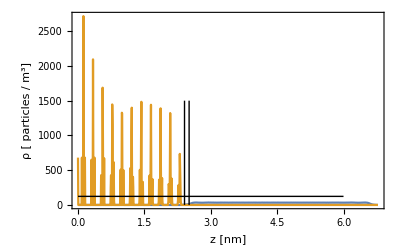

```mathematica
LineGDSSAM5=Line[{{sum5samN,0},{sum5samN,1500}}]
LineDepSAM5=Line[{{sum5samN+depletionDouble5N,0},{sum5samN+depletionDouble5N,1500}}]
LineBulkSAM5=Line[{{0,bulk5surfN},{L5,bulk5surfN}}]
plotNumSAM5=ListPlot[{nWaterData5,nSurfData5},Joined->True,Frame->True,PlotRange->All,GridLines->None,Epilog->{LineGDSSAM5,LineBulkSAM5,LineDepSAM5},FrameLabel->{"z [nm]","ρ [ particles / m^3]"},LabelStyle->{GrayLevel[0]}]
```

```mathematica
SAM 11%
```

We store the water NUMBER density of SAM 11 % in nWaterdata11

```mathematica
input = Import[PathMD<>"ndens_NPT_sam11_water_ptensor.xvg","Table"];
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
nWaterData11 = Take[input,{start+1,Length[input]}]; (* extracted data *)
nWaterData11[[All,2]]=nWaterData11[[All,2]]/3;
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

We store the surface NUMBER density of SAM 11 % in nSurfData11

```mathematica
input = Import[PathMD<>"FINEndens2_NPT_sam11_water_ptensor.xvg","Table"];
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
nSurfData11 = Take[input,{start+1,Length[input]}]; (* extracted data *)
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

We plot the density maps together to determine the bulk intervals. The plot is called plotNum11. We also zoom into the interface region in the plot called plotNum11Zoom.

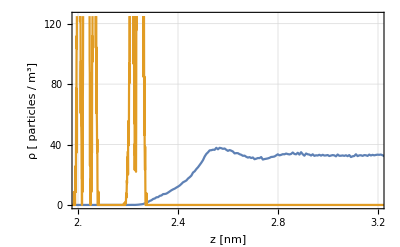

```mathematica
plotNum11=ListPlot[{nWaterData11,nSurfData11},Joined->True,Frame->True,PlotRange->All,GridLines->None];
plotNum11Zoom=ListPlot[{nWaterData11,nSurfData11},Joined->True,PlotRange->{{2,3.2},{0,125}},GridLines->Automatic,Frame->{{True,True},{True,True}},FrameTicks->{{2.0,2.4,2.8,3.2},{0,40,80,120},{None},{None}},FrameLabel->{"z [nm]","ρ [ particles / m^3]"},LabelStyle->{GrayLevel[0]}];
(*GraphicsGrid[{{plotNum11Zoom,plotNum11}}]*)
Show[plotNum11Zoom,Prolog->{Inset[plotNum11,{3.15,0},{Right,Bottom},0.5,Background->White]},PlotLabel->None]
(*PlotStyle->{{Automatic},{Gray}}*)
```

```mathematica
(*Another Way to Use Inset!!!
g=Plot[x ^2,{x,0,100},Prolog->{Inset[plotNum11,{100,200},{Right,Bottom},50]}]*)
```

We calculate the BULK value of the water and the surface as the average of the NON-ZERO density data points. The results are stored in the variables positive11waterN and positive11samN

```mathematica
sum11Nw=0;points=0;Do[If[nWaterData11[[i,2]]≠0,sum11Nw=sum11Nw+nWaterData11[[i,2]];points=points+1],{i,1,Length[nWaterData11]}]
positive11waterN=sum11Nw/points;
Print["water: average of non-negative density = ",positive11waterN]
sum11Ns=0;points=0;Do[If[nSurfData11[[i,2]]≠0,sum11Ns=sum11Ns+nSurfData11[[i,2]];points=points+1],{i,1,Length[nSurfData11]}]
positive11samN=sum11Ns/points;
Print["surface: average of non-negative density = ",positive11samN]
```

water: average of non-negative density = 29.8151

surface: average of non-negative density = 421.821

The MEAN values are stored in the variables mean11waterN and mean11samN

```mathematica
mean11waterN = Mean[nWaterData11[[All,2]]];
Print["water: mean value of number density = ",mean11waterN]
mean11samN = Mean[nSurfData11[[All,2]]];
Print["surface: mean value of number density = ",mean11samN]
```

water: mean value of number density = 20.1252

surface: mean value of number density = 44.8396

The MEAN value of the water density inside an INTERVAL is stored in the variable bulk11waterN . We specifiy the start and end position of the interval.

```mathematica
start=3.5;
end=6;
densDummy=nWaterData11[[All,2]];
posDummy=nWaterData11[[All,1]];
lastPos=posDummy[[-1]]+posDummy[[2]];
intervals=Length[densDummy];
startpos=Round[((start/lastPos)*intervals)+1];
endpos=Round[((end/lastPos)*intervals)+1];
bulk11waterN = Mean[densDummy[[startpos;;endpos]]];
Print["water: mean value of num density = ",bulk11waterN]
```

water: mean value of num density = 32.8163

The MEAN value of the surface density an INTERVAL is stored in the variable bulk11surfN . We specifiy the start and end position of the interval.

```mathematica
start=1.0;
end=2.0;
densDummy=nSurfData11[[All,2]];
posDummy=nSurfData11[[All,1]];
lastPos=posDummy[[-1]]+posDummy[[2]];
intervals=Length[densDummy];
startpos=Round[((start/lastPos)*intervals)+1];
endpos=Round[((end/lastPos)*intervals)+1];
bulk11surfN = Mean[densDummy[[startpos;;endpos]]];
Print["surface: mean value of num density = ",bulk11surfN]
```

surface: mean value of num density = 116.171

INTEGRAL over the WATER is stored in variable sum11waterN.

```mathematica
sum11waterN=Integrate[Interpolation[nWaterData11][x],{x,0,6.0}]/bulk11waterN;
Print["water: Integral/Mean = ",sum11waterN]
```

water: Integral/Mean = 3.59614

```mathematica
L11=Integrate[1,{x,0,6.0}]
```

6.

```mathematica
GDS11N=L11-sum11waterN
```

2.40386

```mathematica
LineGDS11=Line[{{GDS11N,0},{GDS11N,1500}}]
LineBulk11=Line[{{0,bulk11waterN},{3.2,bulk11waterN}}]
```

Line[{{2.40386,0},{2.40386,1500}}]

Line[{{0,32.8163},{3.2,32.8163}}]

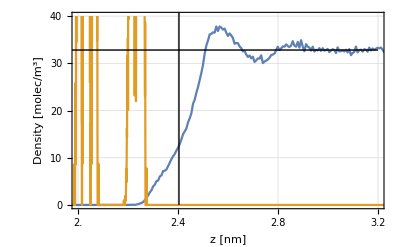

```mathematica
plotNum11GDS=ListPlot[{nWaterData11,nSurfData11},Joined->True,Joined->True,PlotRange->{{2,3.2},{0,40}},GridLines->Automatic,Frame->{{True,True},{True,True}},FrameTicks->{{2.0,2.4,2.8,3.2},{0,10,20,30,40},{None},{None}},FrameLabel->{"z [nm]","Density [molec/m^3]"},LabelStyle->{FontSize->15},Epilog->{LineGDS11,LineBulk11}];
Show[plotNum11GDS,Prolog->{Inset[plotNum0,{3.15,0},{Right,Bottom},0.5,Background->White]},PlotLabel->None]
```

INTEGRAL over the SURFACE is stored in variable sum11samN.

```mathematica
L11=L[[3]]
```

6.67282

```mathematica
sum11samN=Integrate[Interpolation[nSurfData11][x],{x,0,L11}]/bulk11surfN;
Print["surface: Integral/Bulk = ",sum11samN]
```

InterpolatingFunction::dmvali: The integration endpoint 6.67282 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

surface: Integral/Bulk = 2.55178

```mathematica
(*sum11samN=Integrate[Interpolation[nSurfData11][x],{x,0,L11}]/positive11samN;
Print["surface: Integral/Bulk = ",sum11samN]*)
```

surface: Integral/Bulk = 0.932246

The DEPLETION layer is stored in variable d11N.

```mathematica
depletionDouble11N=L11-sum11waterN-sum11samN
```

0.524909

```mathematica
GDS11N-sum11samN
```

-0.147911

```mathematica
d11N=depletionDouble11N/2
```

0.262455

Line[{{2.55178,0},{2.55178,1500}}]

Line[{{3.07668,0},{3.07668,1500}}]

Line[{{0,116.171},{6.67282,116.171}}]

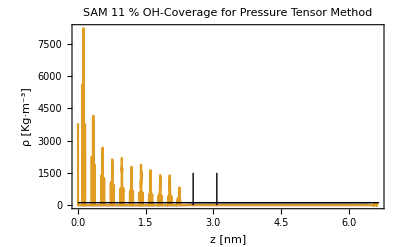

```mathematica
LineGDSSAM11=Line[{{sum11samN,0},{sum11samN,1500}}]
LineDepSAM11=Line[{{sum11samN+depletionDouble11N,0},{sum11samN+depletionDouble11N,1500}}]
LineBulkSAM11=Line[{{0,bulk11surfN},{L11,bulk11surfN}}]
plotNumSAM11=ListPlot[{nWaterData11,nSurfData11},FrameLabel->{"z [nm]","ρ [Kg·m^-3]"},PlotLabel->HoldForm[SAM 11 % OH-Coverage for Pressure Tensor Method],LabelStyle->{GrayLevel[0]},Joined->True,Frame->True,PlotRange->All,GridLines->None,Epilog->{LineGDSSAM11,LineBulkSAM11,LineDepSAM11}]
```

```mathematica
SAM 17%
```

We store the water NUMBER density of SAM 17 % in nWaterdata17

```mathematica
input = Import[PathMD<>"ndens_NPT_sam17_water_ptensor.xvg","Table"];
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
nWaterData17 = Take[input,{start+1,Length[input]}]; (* extracted data *)
nWaterData17[[All,2]]=nWaterData17[[All,2]]/3;
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

We store the surface NUMBER density of SAM 17 % in nSurfData17

```mathematica
input = Import[PathMD<>"ndens2_NPT_sam17_water_ptensor.xvg","Table"];
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
nSurfData17 = Take[input,{start+1,Length[input]}]; (* extracted data *)
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

We plot the density maps together to determine the bulk intervals. The plot is called plotNum17. We also zoom into the interface region in the plot called plotNum17Zoom.

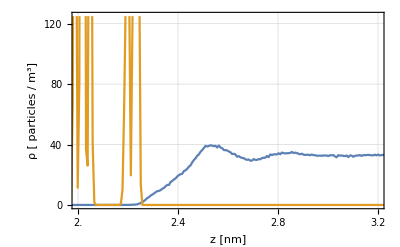

```mathematica
plotNum17=ListPlot[{nWaterData17,nSurfData17},Joined->True,Frame->True,PlotRange->All,GridLines->None];
plotNum17Zoom=ListPlot[{nWaterData17,nSurfData17},Joined->True,PlotRange->{{2,3.2},{0,125}},GridLines->Automatic,Frame->{{True,True},{True,True}},FrameTicks->{{2.0,2.4,2.8,3.2},{0,40,80,120},{None},{None}},FrameLabel->{"z [nm]","ρ [ particles / m^3]"},LabelStyle->{GrayLevel[0]}];
(*GraphicsGrid[{{plotNum17Zoom,plotNum17}}]*)
Show[plotNum17Zoom,Prolog->{Inset[plotNum17,{3.15,0},{Right,Bottom},0.5,Background->White]},PlotLabel->None]
(*PlotStyle->{{Automatic},{Gray}}*)
```

```mathematica
(*Another Way to Use Inset!!!
g=Plot[x ^2,{x,0,100},Prolog->{Inset[plotNum17,{100,200},{Right,Bottom},50]}]*)
```

We calculate the BULK value of the water and the surface as the average of the NON-ZERO density data points. The results are stored in the variables positive17waterN and positive17samN

```mathematica
sum17Nw=0;points=0;Do[If[nWaterData17[[i,2]]≠0,sum17Nw=sum17Nw+nWaterData17[[i,2]];points=points+1],{i,1,Length[nWaterData17]}]
positive17waterN=sum17Nw/points;
Print["water: average of non-negative density = ",positive17waterN]
sum17Ns=0;points=0;Do[If[nSurfData17[[i,2]]≠0,sum17Ns=sum17Ns+nSurfData17[[i,2]];points=points+1],{i,1,Length[nSurfData17]}]
positive17samN=sum17Ns/points;
Print["surface: average of non-negative density = ",positive17samN]
```

water: average of non-negative density = 29.928

surface: average of non-negative density = 347.241

The MEAN values are stored in the variables mean17waterN and mean17samN

```mathematica
mean17waterN = Mean[nWaterData17[[All,2]]];
Print["water: mean value of number density = ",mean17waterN]
mean17samN = Mean[nSurfData17[[All,2]]];
Print["surface: mean value of number density = ",mean17samN]
```

water: mean value of number density = 20.351

surface: mean value of number density = 45.1413

The MEAN value of the water density inside an INTERVAL is stored in the variable bulk17waterN . We specifiy the start and end position of the interval.

```mathematica
start=3.5;
end=6;
densDummy=nWaterData17[[All,2]];
posDummy=nWaterData17[[All,1]];
lastPos=posDummy[[-1]]+posDummy[[2]];
intervals=Length[densDummy];
startpos=Round[((start/lastPos)*intervals)+1];
endpos=Round[((end/lastPos)*intervals)+1];
bulk17waterN = Mean[densDummy[[startpos;;endpos]]];
Print["water: mean value of num density = ",bulk17waterN]
```

water: mean value of num density = 32.8368

The MEAN value of the surface density an INTERVAL is stored in the variable bulk17surfN . We specifiy the start and end position of the interval.

```mathematica
start=1.0;
end=2.0;
densDummy=nSurfData17[[All,2]];
posDummy=nSurfData17[[All,1]];
lastPos=posDummy[[-1]]+posDummy[[2]];
intervals=Length[densDummy];
startpos=Round[((start/lastPos)*intervals)+1];
endpos=Round[((end/lastPos)*intervals)+1];
bulk17surfN = Mean[densDummy[[startpos;;endpos]]];
Print["surface: mean value of num density = ",bulk17surfN]
```

surface: mean value of num density = 115.594

INTEGRAL over the WATER is stored in variable sum17waterN.

```mathematica
sum17waterN=Integrate[Interpolation[nWaterData17][x],{x,0,6.0}]/bulk17waterN;
Print["water: Integral/Mean = ",sum17waterN]
```

water: Integral/Mean = 3.6407

```mathematica
L17=Integrate[1,{x,0,6.0}]
```

6.

```mathematica
GDS17N=L17-sum17waterN
```

2.3593

```mathematica
LineGDS17=Line[{{GDS17N,0},{GDS17N,1500}}]
LineBulk17=Line[{{0,bulk17waterN},{3.2,bulk17waterN}}]
```

Line[{{2.3593,0},{2.3593,1500}}]

Line[{{0,32.8368},{3.2,32.8368}}]

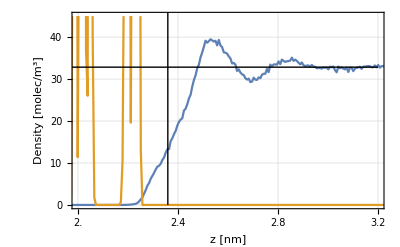

```mathematica
plotNum17GDS=ListPlot[{nWaterData17,nSurfData17},Joined->True,Joined->True,PlotRange->{{2,3.2},{0,45}},GridLines->Automatic,Frame->{{True,True},{True,True}},FrameTicks->{{2.0,2.4,2.8,3.2},{0,10,20,30,40},{None},{None}},FrameLabel->{"z [nm]","Density [molec/m^3]"},LabelStyle->{FontSize->15},Epilog->{LineGDS17,LineBulk17}];
Show[plotNum17GDS,Prolog->{Inset[plotNum17,{3.15,0},{Right,Bottom},0.5,Background->White]},PlotLabel->None]
```

INTEGRAL over the SURFACE is stored in variable sum17samN.

```mathematica
sum17samN=Integrate[Interpolation[nSurfData17][x],{x,0.0,L17}]/bulk17surfN;
Print["surface: Integral/Bulk = ",sum17samN]
```

surface: Integral/Bulk = 2.55318

```mathematica
(*sum17samN=Integrate[Interpolation[nSurfData17][x],{x,0,L17}]/positive17samN;
Print["surface: Integral/Bulk = ",sum17samN]*)
```

surface: Integral/Bulk = 0.849934

The DEPLETION layer is stored in variable d17N.

```mathematica
depletionDouble17N=L17-sum17waterN-sum17samN
```

-0.19388

```mathematica
d17N=depletionDouble17N/2
```

-0.0969399

```mathematica
f1=Interpolation[nSurfData17]
```

InterpolatingFunction[{{0., 6.63395}}, <>]

```mathematica
f2=Interpolation[nWaterData17]
```

InterpolatingFunction[{{0., 6.63395}}, <>]

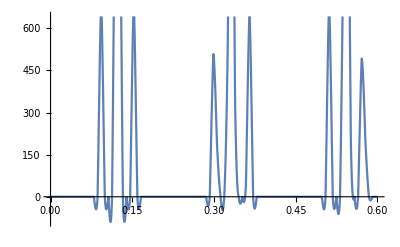

```mathematica
Plot[f1[x],{x,0,0.6}]
```

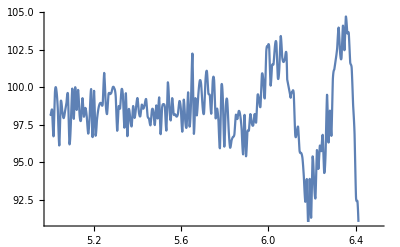

```mathematica
Plot[f2[x],{x,5,6.5}]
```

Line[{{2.55318,0},{2.55318,1500}}]

Line[{{2.3593,0},{2.3593,1500}}]

Line[{{0,115.594},{6.,115.594}}]

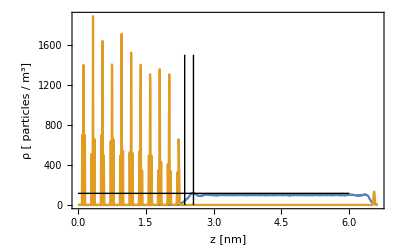

```mathematica
LineGDSSAM17=Line[{{sum17samN,0},{sum17samN,1500}}]
LineDepSAM17=Line[{{sum17samN+depletionDouble17N,0},{sum17samN+depletionDouble17N,1500}}]
LineBulkSAM17=Line[{{0,bulk17surfN},{L17,bulk17surfN}}]
plotNumSAM17=ListPlot[{nWaterData17,nSurfData17},Joined->True,Frame->True,PlotRange->All,GridLines->None,Epilog->{LineGDSSAM17,LineBulkSAM17,LineDepSAM17},FrameLabel->{"z [nm]","ρ [ particles / m^3]"},LabelStyle->{GrayLevel[0]}]
```

```mathematica
SAM 33%
```

We store the water NUMBER density of SAM 33 % in nWaterdata33

```mathematica
input = Import[PathMD<>"ndens_NPT_sam33_water_ptensor.xvg","Table"];
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
nWaterData33 = Take[input,{start+1,Length[input]}]; (* extracted data *)
nWaterData33[[All,2]]=nWaterData33[[All,2]]/3;
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

We store the surface NUMBER density of SAM 33 % in nSurfData33

```mathematica
input = Import[PathMD<>"ndens2_NPT_sam33_water_ptensor.xvg","Table"];
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
nSurfData33 = Take[input,{start+1,Length[input]}]; (* extracted data *)
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

We plot the density maps together to determine the bulk intervals. The plot is called plotNum33. We also zoom into the interface region in the plot called plotNum33Zoom.

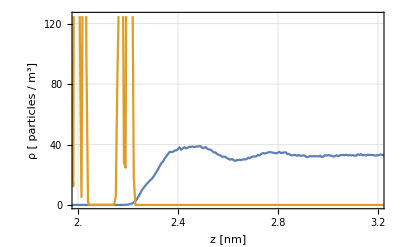

```mathematica
plotNum33=ListPlot[{nWaterData33,nSurfData33},Joined->True,Frame->True,PlotRange->All,GridLines->None];
plotNum33Zoom=ListPlot[{nWaterData33,nSurfData33},Joined->True,PlotRange->{{2,3.2},{0,125}},GridLines->Automatic,Frame->{{True,True},{True,True}},FrameTicks->{{2.0,2.4,2.8,3.2},{0,40,80,120},{None},{None}},FrameLabel->{"z [nm]","ρ [ particles / m^3]"},LabelStyle->{GrayLevel[0]}];
(*GraphicsGrid[{{plotNum33Zoom,plotNum33}}]*)
Show[plotNum33Zoom,Prolog->{Inset[plotNum33,{3.15,0},{Right,Bottom},0.5,Background->White]},PlotLabel->None]
(*PlotStyle->{{Automatic},{Gray}}*)
```

```mathematica
(*Another Way to Use Inset!!!
g=Plot[x ^2,{x,0,100},Prolog->{Inset[plotNum33,{100,200},{Right,Bottom},50]}]*)
```

We calculate the BULK value of the water and the surface as the average of the NON-ZERO density data points. The results are stored in the variables positive33waterN and positive33samN

```mathematica
sum33Nw=0;points=0;Do[If[nWaterData33[[i,2]]≠0,sum33Nw=sum33Nw+nWaterData33[[i,2]];points=points+1],{i,1,Length[nWaterData33]}]
positive33waterN=sum33Nw/points;
Print["water: average of non-negative density = ",positive33waterN]
sum33Ns=0;points=0;Do[If[nSurfData33[[i,2]]≠0,sum33Ns=sum33Ns+nSurfData33[[i,2]];points=points+1],{i,1,Length[nSurfData33]}]
positive33samN=sum33Ns/points;
Print["surface: average of non-negative density = ",positive33samN]
```

water: average of non-negative density = 30.4077

surface: average of non-negative density = 389.458

The MEAN values are stored in the variables mean33waterN and mean33samN

```mathematica
mean33waterN = Mean[nWaterData33[[All,2]]];
Print["water: mean value of number density = ",mean33waterN]
mean33samN = Mean[nSurfData33[[All,2]]];
Print["surface: mean value of number density = ",mean33samN]
```

water: mean value of number density = 20.6468

surface: mean value of number density = 45.5666

The MEAN value of the water density inside an INTERVAL is stored in the variable bulk33waterN . We specifiy the start and end position of the interval.

```mathematica
start=3.5;
end=6;
densDummy=nWaterData33[[All,2]];
posDummy=nWaterData33[[All,1]];
lastPos=posDummy[[-1]]+posDummy[[2]];
intervals=Length[densDummy];
startpos=Round[((start/lastPos)*intervals)+1];
endpos=Round[((end/lastPos)*intervals)+1];
bulk33waterN = Mean[densDummy[[startpos;;endpos]]];
Print["water: mean value of num density = ",bulk33waterN]
```

water: mean value of num density = 32.8705

The MEAN value of the surface density an INTERVAL is stored in the variable bulk33surfN . We specifiy the start and end position of the interval.

```mathematica
start=1.0;
end=2.0;
densDummy=nSurfData33[[All,2]];
posDummy=nSurfData33[[All,1]];
lastPos=posDummy[[-1]]+posDummy[[2]];
intervals=Length[densDummy];
startpos=Round[((start/lastPos)*intervals)+1];
endpos=Round[((end/lastPos)*intervals)+1];
bulk33surfN = Mean[densDummy[[startpos;;endpos]]];
Print["surface: mean value of num density = ",bulk33surfN]
```

surface: mean value of num density = 132.596

INTEGRAL over the WATER is stored in variable sum33waterN.

```mathematica
sum33waterN=Integrate[Interpolation[nWaterData33][x],{x,0,6.0}]/bulk33waterN;
Print["water: Integral/Mean = ",sum33waterN]
```

water: Integral/Mean = 3.7327

```mathematica
L33=Integrate[1,{x,0,6.0}]
```

6.

```mathematica
GDS33N=L33-sum33waterN
```

2.2673

```mathematica
LineGDS33=Line[{{GDS33N,0},{GDS33N,1500}}]
LineBulk33=Line[{{0,bulk33waterN},{3.2,bulk33waterN}}]
```

Line[{{2.2673,0},{2.2673,1500}}]

Line[{{0,32.8705},{3.2,32.8705}}]

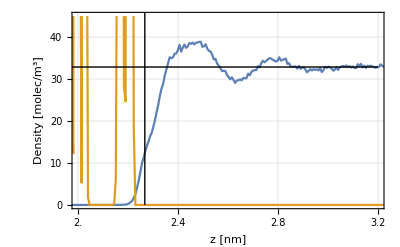

```mathematica
plotNum33GDS=ListPlot[{nWaterData33,nSurfData33},Joined->True,Joined->True,PlotRange->{{2,3.2},{0,45}},GridLines->Automatic,Frame->{{True,True},{True,True}},FrameTicks->{{2.0,2.4,2.8,3.2},{0,10,20,30,40},{None},{None}},FrameLabel->{"z [nm]","Density [molec/m^3]"},LabelStyle->{FontSize->15},Epilog->{LineGDS33,LineBulk33}];
Show[plotNum33GDS,Prolog->{Inset[plotNum33,{3.15,0},{Right,Bottom},0.5,Background->White]},PlotLabel->None]
```

INTEGRAL over the SURFACE is stored in variable sum33samN.

```mathematica
sum33samN=Integrate[Interpolation[nSurfData33][x],{x,0.0,L33}]/bulk33surfN;
Print["surface: Integral/Bulk = ",sum33samN]
```

surface: Integral/Bulk = 2.22389

```mathematica
(*sum33samN=Integrate[Interpolation[nSurfData33][x],{x,0,6.0}]/positive33samN;
Print["surface: Integral/Bulk = ",sum33samN]*)
```

surface: Integral/Bulk = 0.757154

The DEPLETION layer is stored in variable d33N.

```mathematica
depletionDouble33N=L33-sum33waterN-sum33samN
```

0.0434098

```mathematica
d33N=depletionDouble33N/2
```

0.0217049

Line[{{2.22389,0},{2.22389,1500}}]

Line[{{2.2673,0},{2.2673,1500}}]

Line[{{0,132.596},{6.,132.596}}]

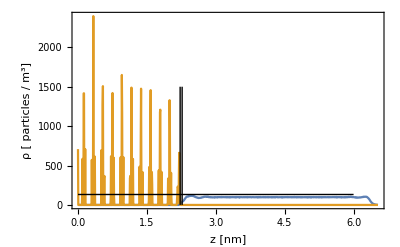

```mathematica
LineGDSSAM33=Line[{{sum33samN,0},{sum33samN,1500}}]
LineDepSAM33=Line[{{sum33samN+depletionDouble33N,0},{sum33samN+depletionDouble33N,1500}}]
LineBulkSAM33=Line[{{0,bulk33surfN},{L33,bulk33surfN}}]
plotNumSAM33=ListPlot[{nWaterData33,nSurfData33},Joined->True,Frame->True,PlotRange->All,GridLines->None,Epilog->{LineGDSSAM33,LineBulkSAM33,LineDepSAM33},FrameLabel->{"z [nm]","ρ [ particles / m^3]"},LabelStyle->{GrayLevel[0]}]
```

```mathematica
SAM 50%
```

```mathematica
With Number Density
```

We store the water NUMBER density of SAM 50 % in nWaterdata50

```mathematica
(*We store the water number density of SAM 50% in nWaterdata50 *)
input = Import[PathMD<>"ndens_NPT_sam50_water_ptensor.xvg","Table"];
(*Length[input]*)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
nWaterData50 = Take[input,{start+1,Length[input]}]; (* extracted data *)
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

We store the surface NUMBER density of SAM 50 % in nSurfData50

```mathematica
(*We store the surface number density of SAM 50% in nSurfData50*)
input = Import[PathMD<>"ndens2_NPT_sam50_water_ptensor.xvg","Table"];
(*Length[input]*)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
nSurfData50 = Take[input,{start+1,Length[input]}]; (* extracted data *)
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

We plot the density maps together to determine the bulk intervals. The plot is called plotNum50. We also zoom into the interface region in the plot called plotNum50Zoom.

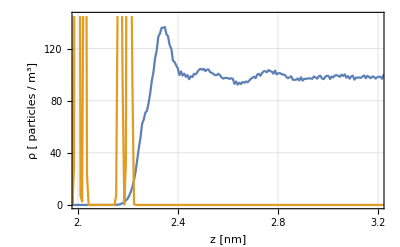

```mathematica
plotNum50=ListPlot[{nWaterData50,nSurfData50},Joined->True,Frame->True,PlotRange->All,GridLines->None];
plotNum50Zoom=ListPlot[{nWaterData50,nSurfData50},Joined->True,PlotRange->{{2,3.2},{0,145}},GridLines->Automatic,Frame->{{True,True},{True,True}},FrameTicks->{{2.0,2.4,2.8,3.2},{0,40,80,120},{None},{None}},FrameLabel->{"z [nm]","ρ [ particles / m^3]"},LabelStyle->{GrayLevel[0]}];
(*GraphicsGrid[{{plotNum0Zoom,plotNum0}}]*)
Show[plotNum50Zoom,Prolog->{Inset[plotNum50,{3.15,0},{Right,Bottom},0.5,Background->White]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
(*PlotStyle->{{Automatic},{Gray}}*)
```

```mathematica
(*Another Way to Use Inset!!!
g=Plot[x ^2,{x,0,100},Prolog->{Inset[plotNum0,{100,200},{Right,Bottom},50]}]*)
```

We calculate the BULK value of the water and the surface as the average of the NON-ZERO density data points. The results are stored in the variables positive50waterN and positive50samN

```mathematica
sum50Nw=0;points=0;Do[If[nWaterData50[[i,2]]≠0,sum50Nw=sum50Nw+nWaterData50[[i,2]];points=points+1],{i,1,Length[nWaterData50]}]
positive50waterN=sum50Nw/points;
Print["water: average of non-negative density = ",positive50waterN]
sum50Ns=0;points=0;Do[If[nSurfData50[[i,2]]≠0,sum50Ns=sum50Ns+nSurfData50[[i,2]];points=points+1],{i,1,Length[nSurfData50]}]
positive50samN=sum50Ns/points;
Print["surface: average of non-negative density = ",positive50samN]
```

water: average of non-negative density = 90.7744

surface: average of non-negative density = 462.181

The MEAN values are stored in the variables mean50waterN and mean50samN

```mathematica
mean50waterN = Mean[nWaterData50[[All,2]]];
Print["water: mean value of number density = ",mean50waterN]
mean50samN = Mean[nSurfData50[[All,2]]];
Print["surface: mean value of number density = ",mean50samN]
```

water: mean value of number density = 62.1804

surface: mean value of number density = 44.8316

The MEAN value of the water density inside an INTERVAL is stored in the variable bulk50waterN . We specifiy the start and end position of the interval.

```mathematica
start=3.5;
end=5.9;
densDummy=nWaterData50[[All,2]];
posDummy=nWaterData50[[All,1]];
lastPos=posDummy[[-1]]+posDummy[[2]];
intervals=Length[densDummy];
startpos=Round[((start/lastPos)*intervals)+1];
endpos=Round[((end/lastPos)*intervals)+1];
bulk50waterN = Mean[densDummy[[startpos;;endpos]]];
Print["water: mean value of num density = ",bulk50waterN]
```

water: mean value of num density = 98.3659

The MEAN value of the surface density an INTERVAL is stored in the variable bulk50surfN . We specifiy the start and end position of the interval.

```mathematica
start=1.0;
end=2.0;
densDummy=nSurfData50[[All,2]];
posDummy=nSurfData50[[All,1]];
lastPos=posDummy[[-1]]+posDummy[[2]];
intervals=Length[densDummy];
startpos=Round[((start/lastPos)*intervals)+1];
endpos=Round[((end/lastPos)*intervals)+1];
bulk50surfN = Mean[densDummy[[startpos;;endpos]]];
Print["surface: mean value of num density = ",bulk50surfN]
```

surface: mean value of num density = 127.422

INTEGRAL over the WATER is stored in variable sum50waterN.

```mathematica
sum50waterN=Integrate[Interpolation[nWaterData50][x],{x,0,5.9}]/bulk50waterN;
Print["water: Integral/Mean = ",sum50waterN]
```

water: Integral/Mean = 3.67758

```mathematica
L50=Integrate[1,{x,0,5.9}]
```

5.9

```mathematica
GDS50N=L50-sum50waterN
```

2.22242

```mathematica
LineGDS50=Line[{{GDS50N,0},{GDS50N,1500}}]
LineBulk50=Line[{{0,bulk50waterN},{3.2,bulk50waterN}}]
```

Line[{{2.22242,0},{2.22242,1500}}]

Line[{{0,98.3659},{3.2,98.3659}}]

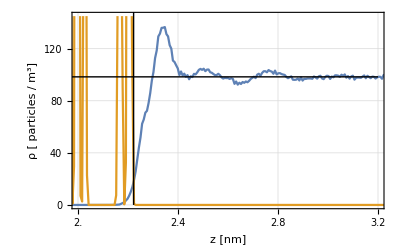

```mathematica
plotNum50GDS=ListPlot[{nWaterData50,nSurfData50},Joined->True,PlotRange->{{2,3.2},{0,145}},GridLines->Automatic,Frame->{{True,True},{True,True}},FrameTicks->{{2.0,2.4,2.8,3.2},{0,40,80,120},{None},{None}},FrameLabel->{"z [nm]","ρ [ particles / m^3]"},LabelStyle->{GrayLevel[0]},Epilog->{LineBulk50,LineGDS50}]
```

INTEGRAL over the SURFACE is stored in variable sum50samN.

```mathematica
sum50samN=Integrate[Interpolation[nSurfData50][x],{x,0.0,L50}]/bulk50surfN;
Print["surface: Integral/Bulk = ",sum50samN]
```

surface: Integral/Bulk = 2.2913

```mathematica
(*sum50samN=Integrate[Interpolation[nSurfData50][x],{x,0,L50}]/positive50samN;
Print["surface: Integral/Bulk = ",sum50samN]*)
```

surface: Integral/Bulk = 0.631707

The DEPLETION layer is stored in variable d50N.

```mathematica
depletionDouble50N=L50-sum50waterN-sum50samN
```

-0.0688831

```mathematica
d50N=depletionDouble50N/2
```

-0.0344415

Line[{{2.2913,0},{2.2913,1500}}]

Line[{{2.22242,0},{2.22242,1500}}]

Line[{{0,127.422},{5.9,127.422}}]

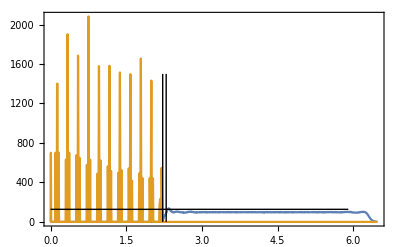

```mathematica
LineGDSSAM50=Line[{{sum50samN,0},{sum50samN,1500}}]
LineDepSAM50=Line[{{sum50samN+depletionDouble50N,0},{sum50samN+depletionDouble50N,1500}}]
LineBulkSAM50=Line[{{0,bulk50surfN},{L50,bulk50surfN}}]
plotNumSAM50=ListPlot[{nWaterData50,nSurfData50},Joined->True,Frame->True,PlotRange->All,GridLines->None,Epilog->{LineGDSSAM50,LineBulkSAM50,LineDepSAM50}]
```

```mathematica
SAM 66%
```

```mathematica
With Number Density
```

We store the water NUMBER density of SAM 66 % in nWaterdata66

```mathematica
input = Import[PathMD<>"ndens_NPT_sam66_water_ptensor.xvg","Table"];
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
nWaterData66 = Take[input,{start+1,Length[input]}]; (* extracted data *)
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

We store the surface NUMBER density of SAM 66 % in nSurfData66

```mathematica
input = Import[PathMD<>"ndens2_NPT_sam66_water_ptensor.xvg","Table"];
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
nSurfData66 = Take[input,{start+1,Length[input]}]; (* extracted data *)
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

We plot the density maps together to determine the bulk intervals. The plot is called plotNum66. We also zoom into the interface region in the plot called plotNum66Zoom.

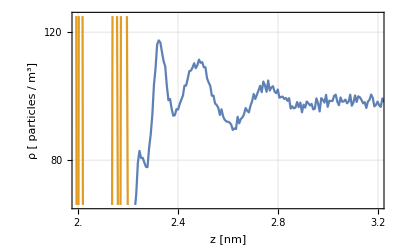

```mathematica
plotNum66=ListPlot[{nWaterData66,nSurfData66},Joined->True,Frame->True,PlotRange->All,GridLines->None];
plotNum66Zoom=ListPlot[{nWaterData66,nSurfData66},Joined->True,PlotRange->{{2,3.2},{66,125}},GridLines->Automatic,Frame->{{True,True},{True,True}},FrameTicks->{{2.0,2.4,2.8,3.2},{0,40,80,120},{None},{None}},FrameLabel->{"z [nm]","ρ [ particles / m^3]"},LabelStyle->{GrayLevel[0]},LabelStyle->{GrayLevel[0],Bold}];
(*GraphicsGrid[{{plotNum66Zoom,plotNum66}}]*)
Show[plotNum66Zoom,Prolog->{Inset[plotNum66,{3.15,65},{Right,Bottom},0.5,Background->White]},PlotLabel->None]
(*PlotStyle->{{Automatic},{Gray}}*)
```

```mathematica
(*Another Way to Use Inset!!!
g=Plot[x ^2,{x,0,100},Prolog->{Inset[plotNum66,{100,200},{Right,Bottom},50]}]*)
```

We calculate the BULK value of the water and the surface as the average of the NON-ZERO density data points. The results are stored in the variables positive66waterN and positive66samN

```mathematica
sum66Nw=0;points=0;Do[If[nWaterData66[[i,2]]≠0,sum66Nw=sum66Nw+nWaterData66[[i,2]];points=points+1],{i,1,Length[nWaterData66]}]
positive66waterN=sum66Nw/points;
Print["water: average of non-negative density = ",positive66waterN]
sum66Ns=0;points=0;Do[If[nSurfData66[[i,2]]≠0,sum66Ns=sum66Ns+nSurfData66[[i,2]];points=points+1],{i,1,Length[nSurfData66]}]
positive66samN=sum66Ns/points;
Print["surface: average of non-negative density = ",positive66samN]
```

water: average of non-negative density = 91.8562

surface: average of non-negative density = 422.914

The MEAN values are stored in the variables mean66waterN and mean66samN

```mathematica
mean66waterN = Mean[nWaterData66[[All,2]]];
Print["water: mean value of number density = ",mean66waterN]
mean66samN = Mean[nSurfData66[[All,2]]];
Print["surface: mean value of number density = ",mean66samN]
```

water: mean value of number density = 62.7378

surface: mean value of number density = 45.6747

The MEAN value of the water density inside an INTERVAL is stored in the variable bulk66waterN . We specifiy the start and end position of the interval.

```mathematica
start=3.5;
end=6;
densDummy=nWaterData66[[All,2]];
posDummy=nWaterData66[[All,1]];
lastPos=posDummy[[-1]]+posDummy[[2]];
intervals=Length[densDummy];
startpos=Round[((start/lastPos)*intervals)+1];
endpos=Round[((end/lastPos)*intervals)+1];
bulk66waterN = Mean[densDummy[[startpos;;endpos]]];
Print["water: mean value of num density = ",bulk66waterN]
```

water: mean value of num density = 98.416

The MEAN value of the surface density an INTERVAL is stored in the variable bulk66surfN . We specifiy the start and end position of the interval.

```mathematica
start=1.0;
end=2.0;
densDummy=nSurfData66[[All,2]];
posDummy=nSurfData66[[All,1]];
lastPos=posDummy[[-1]]+posDummy[[2]];
intervals=Length[densDummy];
startpos=Round[((start/lastPos)*intervals)+1];
endpos=Round[((end/lastPos)*intervals)+1];
bulk66surfN = Mean[densDummy[[startpos;;endpos]]];
Print["surface: mean value of num density = ",bulk66surfN]
```

surface: mean value of num density = 136.775

INTEGRAL over the WATER is stored in variable sum66waterN.

```mathematica
sum66waterN=Integrate[Interpolation[nWaterData66][x],{x,0,6.0}]/bulk66waterN;
Print["water: Integral/Mean = ",sum66waterN]
```

water: Integral/Mean = 3.79487

```mathematica
L66=Integrate[1,{x,0,6.0}]
```

6.

```mathematica
GDS66N=L66-sum66waterN
```

2.20513

```mathematica
LineGDS66=Line[{{GDS66N,0},{GDS66N,1500}}]
LineBulk66=Line[{{0,bulk66waterN},{3.2,bulk66waterN}}]
```

Line[{{2.20513,0},{2.20513,1500}}]

Line[{{0,98.416},{3.2,98.416}}]

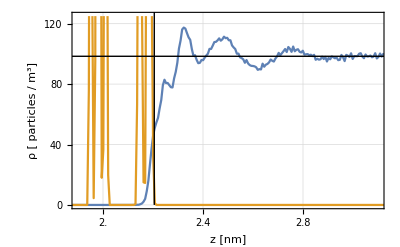

```mathematica
plotNum66GDS=ListPlot[{nWaterData66,nSurfData66},Joined->True,PlotRange->{{1.9,3.1},{0,125}},GridLines->Automatic,Frame->{{True,True},{True,True}},FrameTicks->{{2.0,2.4,2.8,3.2},{0,40,80,120},{None},{None}},FrameLabel->{"z [nm]","ρ [ particles / m^3]"},LabelStyle->{GrayLevel[0]},Epilog->{LineGDS66,LineBulk66}]
```

INTEGRAL over the SURFACE is stored in variable sum66samN.

```mathematica
sum66samN=Integrate[Interpolation[nSurfData66][x],{x,0.0,L66}]/bulk66surfN;
Print["surface: Integral/Bulk = ",sum66samN]
```

surface: Integral/Bulk = 2.14896

```mathematica
sum66samN=Integrate[Interpolation[nSurfData66][x],{x,0,L66}]/positive66samN;
Print[(*"surface: Integral/Bulk = "*),sum66samN]
```

Null0.694999

The DEPLETION layer is stored in variable d66N.

```mathematica
depletionDouble66N=L66-sum66waterN-sum66samN
```

1.51013

```mathematica
d66N=depletionDouble66N/2
```

0.755066

Line[{{0.694999,0},{0.694999,1500}}]

Line[{{2.20513,0},{2.20513,1500}}]

Line[{{0,136.775},{6.,136.775}}]

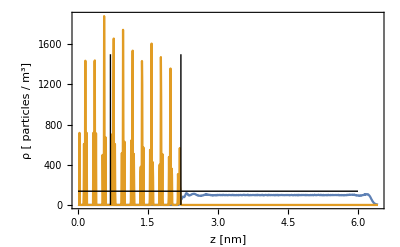

```mathematica
LineGDSSAM66=Line[{{sum66samN,0},{sum66samN,1500}}]
LineDepSAM66=Line[{{sum66samN+depletionDouble66N,0},{sum66samN+depletionDouble66N,1500}}]
LineBulkSAM66=Line[{{0,bulk66surfN},{L66,bulk66surfN}}]
plotNumSAM66=ListPlot[{nWaterData66,nSurfData66},Joined->True,Frame->True,PlotRange->All,GridLines->None,Epilog->{LineGDSSAM66,LineBulkSAM66,LineDepSAM66},FrameLabel->{"z [nm]","ρ [ particles / m^3]"},LabelStyle->{GrayLevel[0]}]
```

```mathematica
SAM 0%
```

```mathematica
With Mass Density
```

```mathematica
(*We store the water mass density of SAM 0% in Waterdata0*)
input = Import[PathMD<>"dens_NPT_sam0_water_ptensor.xvg","Table"];
(*Length[input]*)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData0 = Take[input,{start+1,Length[input]}]; (* extracted data *)
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

```mathematica
(*We store the surface mass density of SAM 0% in SurfData0*)
input = Import[PathMD<>"dens2_NPT_sam0_water_ptensor.xvg","Table"];
(*Length[input]*)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData0 = Take[input,{start+1,Length[input]}]; (* extracted data *)
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

```mathematica
waterplot0=ListPlot[WaterData0,Joined->True,PlotStyle->{Red,Thick}];
surfplot0=ListPlot[SurfData0,Joined->True];
plotMass0=Show[waterplot0,surfplot0,PlotLabel->"Mass Density SAM 0%",AxesLabel->{"z[nm]","ρ[kg/m3]"},Frame->True,PlotRange->All];
```

```mathematica
sum0s=0;points=0;Do[If[SurfData0[[i,2]]≠0,sum0s=sum0s+SurfData0[[i,2]];points=points+1],{i,1,Length[SurfData0]}]
bulk0surf=sum0s/points
```

2860.21

```mathematica
sum0w=0;points=0;Do[If[WaterData0[[i,2]]≠0,sum0w=sum0w+WaterData0[[i,2]];points=points+1],{i,1,Length[WaterData0]}]
bulk0water=sum0w/points
```

891.276

```mathematica
mean0sam = Mean[SurfData0];
Print["surface: mean value of num density = ",mean0sam]
```

surface: mean value of num density = {3.38607,320.344}

surface: mean value of num density = Mean[SurfData0]⟦All,2⟧

surface: mean value of num density = 346.205

```mathematica
mean0water = Mean[WaterData0]
Print["water: mean value of num density = ",mean0water]
```

{3.38607,595.372}

water: mean value of num density = {3.38607,595.372}

```mathematica
sum0sam=Integrate[Interpolation[SurfData0][x],{x,0.0,L[[6]]}]/bulk0surf
Print["surface: Integral/Bulk = ",sum0sam]
```

0.757449

surface: Integral/Bulk = 0.757449

```mathematica
sum0water=Integrate[Interpolation[WaterData0][x],{x,0,L[[6]]}]/bulk0water
```

4.39063

```mathematica
(*SECOND TRY*)
sum0water=Integrate[Interpolation[WaterData0][x],{x,0,L[[6]]}]/980
```

3.99312

```mathematica
L0=Integrate[1,{x,0,L[[6]]}]
```

6.49091

```mathematica
total0=L0-sum0water-sum0sam
```

1.41984

```mathematica
d0=total0/2
```

0.709919

```mathematica
L0-sum0water
```

2.49779

```mathematica
GraphicsRow[{plotMass0,plotNum0}]
```

-Graphics-

```mathematica
SAM 5%
```

```mathematica
SAM 11%
```

```mathematica
SAM 17%
```

```mathematica
SAM 33%
```

```mathematica
SAM 50%
```

```mathematica
With Mass Density
```

```mathematica
(*We store the water mass density of SAM 50% in Waterdata50*)
input = Import[PathMD<>"dens_NPT_sam50_water_ptensor.xvg","Table"];
(*Length[input]*)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData50 = Take[input,{start+1,Length[input]}]; (* extracted data *)
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

```mathematica
(*We store the surface mass density of SAM 50% in SurfData50*)
input = Import[PathMD<>"dens2_NPT_sam50_water_ptensor.xvg","Table"];
(*Length[input]*)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData50 = Take[input,{start+1,Length[input]}]; (* extracted data *)
(*slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; *)
```

```mathematica
sum50s=0;points=0;Do[If[SurfData50[[i,2]]≠0,sum50s=sum50s+SurfData50[[i,2]];points=points+1],{i,1,Length[SurfData50]}]
bulk50surf=sum50s/points
```

3569.12

```mathematica
sum50w=0;points=0;Do[If[WaterData50[[i,2]]≠0,sum50w=sum50w+WaterData50[[i,2]];points=points+1],{i,1,Length[WaterData50]}]
bulk50water=sum50w/points
```

905.182

```mathematica
mean50sam = Mean[SurfData50][[2]];
Print["surface: mean value of num density = ",mean50sam]
```

surface: mean value of num density = 346.205

```mathematica
mean50water = Mean[WaterData50][[2]]
Print["water: mean value of num density = ",mean50water]
```

620.05

water: mean value of num density = 620.05

```mathematica
sum50sam=Integrate[Interpolation[SurfData50][x],{x,0.0,L[[6]]}]/bulk50surf
Print["surface: Integral/Bulk = ",sum50sam]
```

InterpolatingFunction::dmvali: The integration endpoint 6.49091 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

0.629442

surface: Integral/Bulk = 0.629442

```mathematica
sum50water=Integrate[Interpolation[WaterData50][x],{x,0,L[[6]]}]/bulk50water
```

InterpolatingFunction::dmvali: The integration endpoint 6.49091 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

4.44163

```mathematica
L50=Integrate[1,{x,0,L[[6]]}]
```

6.49091

```mathematica
total50=L50-sum50water-sum50sam
```

1.41984

```mathematica
d50=total50-total0N
```

0.709919

```mathematica
GraphicsRow[{plotMass50,plotNum50}]
```

-Graphics-

```mathematica
SAM 66%
```